# Oblique asymptote

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[x_]:=(x^2+3)/(x+1)
```

```mathematica
Limit[f[x],x->∞]
```

∞

```mathematica
m=Limit[f[x]/x,x->∞]
```

1

```mathematica
b=Limit[f[x]-m x,x->∞]
```

-1

```mathematica
obliqueAsymptote=m x+b
```

-1+x

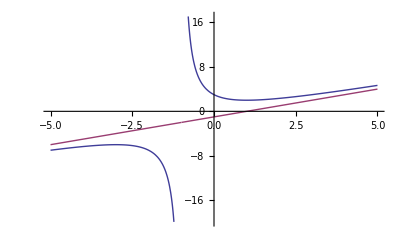

```mathematica
Plot[{f[x],obliqueAsymptote},{x,-5,5},Exclusions->-1]
```